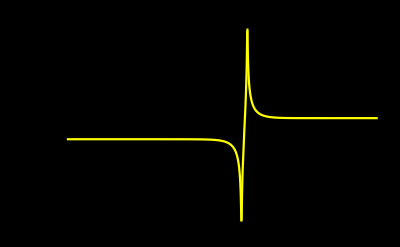

```mathematica
R1 = 0.1;
R2 = 1000;
R3 = 0.1;
R4 = 1000;

L1 = 10^-3;
L2 = 10^-3;

C1 = 10^-6;
C2 = 10^-6;

(* R1 a zC1 se spojí do z1
 R2 a zL1 se spojí do z2
z1 a z2 se paralelně spojí do z3

R4 a zC2 se paralelně spojí do z4
z3, zL2 a z4 se spojí do Zc *)

zC1 = 1/(ⅉ*ω*C1);
z1 = R1 + zC1;
zL1 = ⅉ*ω*L1;
z2 = R2+ zL1;

z3 = 1/(1/z1+1/z2);

zC2 = 1/(ⅉ*ω*C2);
zL2 = ⅉ*ω*L2;
z4 = 1/(1/R4+1/zC2);
z5 = zL2 + z4;
Z = z3 + z5;

(* Teď chci poměr z5 ku z3 + z5 *)
A = z5/(z3 + z5);
LogLogPlot[Abs[A], {ω, 1, 10^8}, PlotRange -> All, Background -> Black, PlotStyle -> Yellow, PlotLabel -> "A[ω]"]
```